```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo2.txt", "Table"];
```

dataLength will be 1000, this was just an experiment

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
cleanData;
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0}}

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,89},{1,78},{2,73},{3,58},{4,65},{5,51},{6,57},{7,55},{8,54},{9,35},{10,23},{11,30},{12,35},{13,35},{14,17},{15,23},{16,25},{17,23},{18,12},{19,6},{20,18},{21,15},{22,9},{23,17},{24,7},{25,12},{26,7},{27,5},{28,7},{29,9},{30,5},{31,3},{32,8},{33,1},{34,3},{35,3},{36,1},{37,8},{38,1},{39,3},{40,3},{41,2},{42,1},{43,0},{44,1},{45,0},{46,0},{47,0},{48,1},{49,1},{50,0},{51,1},{52,0},{53,0},{54,0},{55,1},{56,0},{57,0},{58,1},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,1},{66,1}}

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

9.938

```mathematica
probDensFunc[x_]:=N[probabilityData[[x+1,2]]/dataLength]
```

```mathematica
probDensFunc[0]
```

0.089

http://math.bme.hu/~nandori/Virtual_lab/stat/expect/Generating.pdf

```mathematica
probGenFunc[z_]:=Sum[probDensFunc[n]*(z^n),{n,0,Max[cleanData]}]
```

```mathematica
probGenFunc[0.01]
```

0.0897874

General::munfl: 0.001 1.46376×10^-305 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

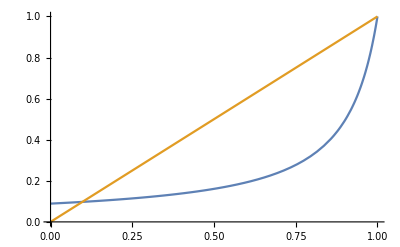

```mathematica
Plot[{probGenFunc[t],t},{t,0,1}]
```

```mathematica
probGenFunc[0.2687]
```

0.116793

```mathematica
cleanData;
```

```mathematica
DistributionFitTest[cleanData,GeometricDistribution[probabilityData[[1,2]]/1000],"HypothesisTestData"]["TestDataTable",All]
```

| Statistic | P-Value
Pearson χ^2 | 32.8934 | 0.0633895

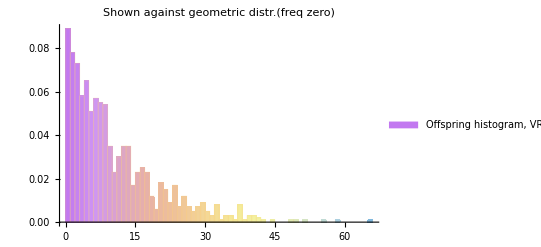

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartLegends->{"Offspring histogram, VRR=2*E-3."},ChartStyle->"Pastel",PlotLabel->"Shown against geometric distr.(freq zero)"]
```

```mathematica
probabilityData[[1,2]]
```

89

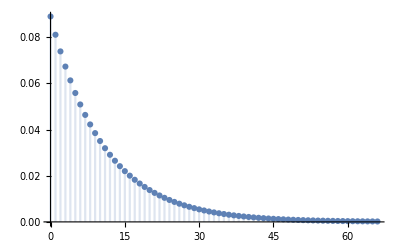

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic]
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-